### Two-mode Squeezed state as input 2019/08/30 2019/07/04 2019/06/24 2019/06/04

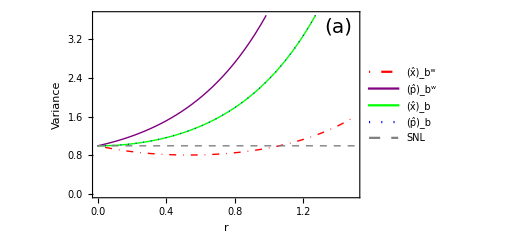

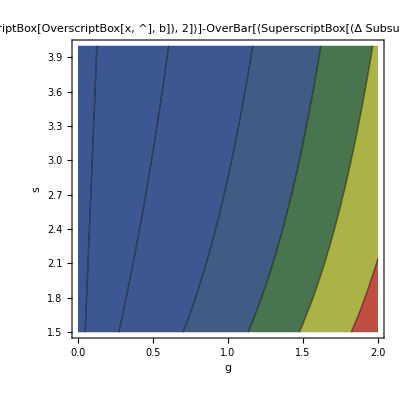

```mathematica
cleanContourPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,_Tooltip,Infinity];
Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]]

cleanContourPlot[Legended[cp_Graphics,rest___]]:=Legended[cleanContourPlot[cp],rest];
n=50;(* number od modes *)
T=1/(n s);
fX2=1+2 n T(Sinh[r]^2);(* Without wavefront shaping*)
fP2=1+2 n T(Sinh[r]^2);(* Without wavefront shaping*)
flucX2=1+2 n T Sinh[r](Sinh[r]-π/4 Cosh[r]);(* With wavefront shaping*)
flucP2=1+2 n T Sinh[r](Sinh[r]+π/4 Cosh[r]);(* With wavefront shaping*)
fig2=Plot[{flucX2/.s->2,flucP2/.s->2,fX2/.s->2,fP2/.s->2,r-r+1},{r,0,1.5},PlotStyle->{{DotDashed,Red,Thick},{Purple,Thick},{Green,Thick},{Dotted,Blue,Thick},{Gray,Dashed,Thick}},PlotLegends->Placed[{Style["(x̂)_b^w",FontSize->14],Style["(p̂)_b^w",FontSize->14],Style["(x̂)_b",FontSize->14],Style["(p̂)_b",FontSize->14],Style["SNL",FontSize->12.5]},{{0.13,0.7}}],Frame->True, FrameLabel->{Style["r",FontSize->20],Text[Style["Variance",FontSize->20]]},FrameTicksStyle->Directive[14.5],PlotRange->{{0,3.7}},Epilog->{Text[Style["(a)",FontSize->20],Scaled[{.92,.92}]](*,Text[Style["SNL",FontSize->14],Scaled[{.88,.33}]],Text[Style["(x̂)_b^w",FontSize->14],Scaled[{.6,.08}]],Text[Style["(p̂)_b^w",FontSize->14],Scaled[{.45,.88}]],,Text[Style["(x̂)_b",FontSize->14],Scaled[{.9,.88}]],Text[Style["(p̂)_b",FontSize->14],Scaled[{.82,.7}]]*)},ImageSize->{380,280}]
(*fig2=Plot[{fX2/.s->2,flucX2/.s->2,1+r-r},{r,0,1.5},PlotStyle->{{Blue,Thick},{DotDashed,Red,Thick},{Gray,Dashed,Thick}},PlotLegends->Placed[{Style["Without WFS",FontSize->14],Style["With WFS",FontSize->14],Style["SNL",FontSize->14]},{{0.25,0.7}}],Frame->True, FrameLabel->{Style["g",FontSize->20],Text[Style["OverBar[⟨SuperscriptBox[(ΔOverscriptBox[x, ^]), 2]⟩]",FontSize->20]]},FrameTicksStyle->Directive[14.5],PlotRange->{{0.5,3}},Epilog->{Text[Style["(a)",FontSize->20],Scaled[{.066,.92}]]},ImageSize->{380,280}]*)
(*fig2a=Plot3D[flucX2-fX2,{r,0,2},{s,1,4},ColorFunction->"SolarColors",AxesLabel->{Style["g",FontSize->20],Style["s",FontSize->20],Rotate[Style["OverBar[⟨SuperscriptBox[(ΔSubsuperscriptBox[OverscriptBox[x, ^], b, w]), 2]⟩]-OverBar[⟨SuperscriptBox[(ΔSubscriptBox[OverscriptBox[x, ^], b]), 2]⟩]",FontSize->15,Bold],90 Degree]},PlotRange->All]*)
(*fig2b=ContourPlot[fX2-flucX2,{r,0,2},{s,1,4},PlotRange->All,ColorFunction->ColorData[{"SolarColors","Reverse"}],Contours->{0.2,1,10,20,30},ContourLabels->All,Frame->True, FrameLabel->{Style["g",FontSize->20],Text[Style["s",FontSize->20]]},PlotLabel->Style["OverBar[⟨SuperscriptBox[(ΔSubscriptBox[OverscriptBox[x, ^], b]), 2]⟩]-OverBar[⟨SuperscriptBox[(ΔSubsuperscriptBox[OverscriptBox[x, ^], b, w]), 2]⟩]",FontSize->15]]*)
fig2b0=ContourPlot[fX2-flucX2,{r,0,2},{s,1.5,4},PlotRange->All,ColorFunction->"DarkRainbow",Frame->True, FrameLabel->{Style["g",FontSize->28],Text[Style["s",FontSize->28]]},FrameTicksStyle->Directive[20],PlotLabel->Style["OverBar[⟨SuperscriptBox[(Δ SubscriptBox[OverscriptBox[x, ^], b]), 2]⟩]-OverBar[⟨SuperscriptBox[(Δ SubsuperscriptBox[OverscriptBox[x, ^], b, w]), 2]⟩]",FontSize->20],Contours->{0.05,0.3,1,2.5,5,10,15,20,25,30},PlotLegends->BarLegend[Automatic,LegendMarkerSize->240,LegendFunction->"Frame",LegendMargins->5,LabelStyle->{FontSize->16}]];
fig2b=cleanContourPlot[fig2b0]
```

```mathematica
(*Export["E:\\MT\\00_Researching\\03_PUF\\03_Security_PUF\\05_New_scheme\\09_Squeezing_focused_light\\03_Code\\00_Figures\\dx2r_2modes20190624.eps",fig2]*)(*ImageResolution->300,ImageSize->{480,480}];*)
Export["E:\\MT\\00_Researching\\03_PUF\\03_Security_PUF\\05_New_scheme\\09_Squeezing_focused_light\\03_Code\\00_Figures\\3Dsqz2_20190708.eps",fig2b]
```

E:\MT\00_Researching\03_PUF\03_Security_PUF\05_New_scheme\09_Squeezing_focused_light\03_Code\00_Figures\3Dsqz2_20190708.eps

```mathematica
∫_0^∞ x/a^2 ⅇ^(-x^2/(2 a^2))ⅆx
```

ConditionalExpression[1,Re[a^2]>0]

```mathematica
f1=Simplify[∫_0^∞ x^(3/2)/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

2^(1/4) √a Gamma[5/4]

a √(π/2)

2 a^2

π/4

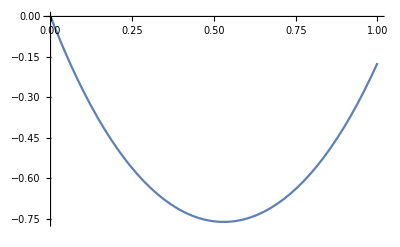

```mathematica
f2=Simplify[∫_0^∞ x^2/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
f4=Simplify[∫_0^∞ x^3/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
ratio=f2^2/f4  
diff=4Sinh[r](Sinh[r]-ratio Cosh[r]);
Plot[diff,{r,0,1}]
```

```mathematica
f4=Simplify[∫_0^∞ x^3/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

2 a^2

```mathematica
f6=Simplify[∫_0^∞ x^5/a^2 ⅇ^(-x^2/(2 a^2))ⅆx,Assumptions->{a>0}]
```

8 a^4

```mathematica
f6/f4^2
```

2

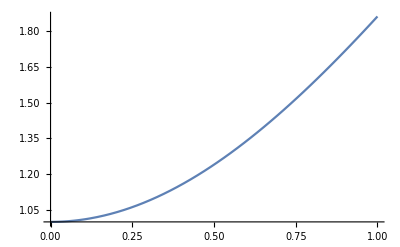

```mathematica
g=1/2 ⅇ^(-a^2) (2+a ⅇ^(a^2) √π+a ⅇ^(a^2) √π Erf[a]-a ⅇ^(a^2) √π Erfc[a]);
Plot[g,{a,0,1}]
```

1/2 (1+2 a^2) √π

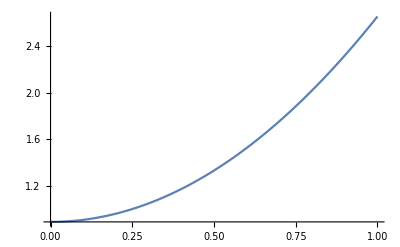

```mathematica
f1=1/(√π)∫_(-∞)^∞ x^2 ⅇ^(-(x-a)^2)ⅆx
Plot[f1,{a,0,1}]
```

```mathematica
norm=1/(√π)∫_(-∞)^∞ ⅇ^(-(x-a)^2)ⅆx
```

√π

1/4 (3+4 a^2 (3+a^2)) √π

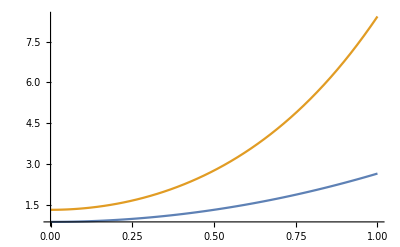

```mathematica
f2=∫_(-∞)^∞ x^4 ⅇ^(-(x-a)^2)ⅆx
Plot[{f1,f2},{a,0,1}]
```

```mathematica
√π f2/f1^2//Expand
```

3/((1+2 a^2)^2)+(12 a^2)/((1+2 a^2)^2)+(4 a^4)/((1+2 a^2)^2)

```mathematica
Sinh[x]/Cosh[x]
```

```mathematica
Tanh[x]
```

```mathematica
ArcTanh[Pi/8]//N
```

0.414987